# Graphics for Fish Paper for AJP - Jevin Jensen & YLL

Some of this is superseded by RefractionSimulations.nb, which is to be submitted as EPAPS Supplementary Information.

## Section Snell’s Law geometrical construction

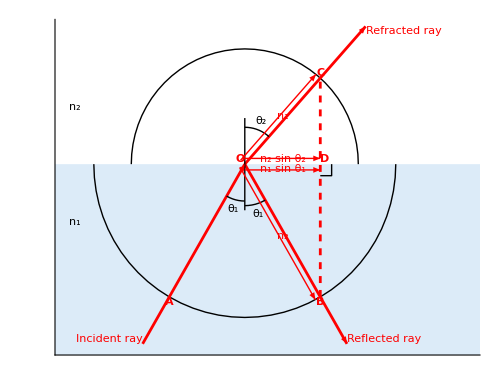

```mathematica
(*--------  User-defined parameters (play with these) ------*)
n1=1.33;n2=1;Z1=1./n1;Z2=1./n2;(* refractive indices of media *)
θ1=30°;
θ2=ArcSin[n1/n2*Sin@θ1];
(*--------  Code ------*)
k1hat={Sin@θ1,Cos@θ1};k3hat={Sin@θ1,-Cos@θ1};k2hat={Sin@θ2,Cos@θ2};
rO={0,0};
rA=n1{-Sin@θ1,-Cos@θ1};rB=n1{+Sin@θ1,-Cos@θ1};rC=n2{+Sin@θ2,+Cos@θ2};rD=n2{+Sin@θ2,0};
SetOptions[Graphics,BaseStyle->16];
rayLen=1.8;len3=1.6;raySty=Directive[Red,AbsoluteThickness@2];nrmLen=.4;
waterColor=RGBColor[{0.8627450980392157,0.9215686274509803,0.9725490196078431}];
cross[{kx_,ky_}]:={-ky,kx};
grAH=Graphics[Line[{{-1,1},{2,0},{-1,-1}}]];
gr=Graphics[{
(*-------- water --------*)
{waterColor,Rectangle[{-999,0},{999,-999}]},
(*-------- circles and rays --------*)
Circle[{0,0},n1,{-π,0}],
Circle[{0,0},n2,{0,π}],
AbsolutePointSize@9,
raySty,
Arrowheads[{{.03,0.1}}],  (* settings *)
Arrow[{-rayLen*k1hat,{0,0}}],(* incident ray *)
Arrowheads[{{.03,1.}}],  (* settings *)
Arrow[{{0,0},len3*k2hat}],(* refracted ray *)
Arrow[{{0,0},rayLen*k3hat}],(* reflected ray *)
Black,AbsoluteThickness@1,
Line@{{0,0},nrmLen{0,1}},  (* upward normal *)
Line@{{0,0},nrmLen{0,-1}},  (* downward normal *)
Circle[{0,0},.8nrmLen,{π/2-θ2,π/2}], (* top arc *)
Text["θ_2",nrmLen{Sin[θ2/2],Cos[θ2/2]}],(* refracted angle *)
Circle[{0,0},.8nrmLen,{-π/2,-π/2-θ1}], (* incident angle arc *)
Text["θ_1",nrmLen{-Sin[θ1/2],-Cos[θ1/2]}],(* incident angle *)
nrmLen+=.05;
Circle[{0,0},.8nrmLen,{-π/2,-π/2+θ1}], (* reflected angle arc *)
Text["θ_1",nrmLen{+Sin[θ1/2],-Cos[θ1/2]}],(* reflected angle arc angle *)
(*-------- vertical construction line --------*)
{raySty,Dashed,Line@{n1{+Sin@θ1,-Cos@θ1},n2{+Sin@θ2,+Cos@θ2}}},
(*-------- dimension lines --------*)
Arrowheads[{{-.02,0},{.02,1}}],
Black,
Line@{{rD+.1{1,0},rD+.1{1,-1},rD-.1{0,1}}},(* 90 degree angles *)
(*Line@{{rD-.1{1,0},rD-.1{1,1},rD-.1{0,1}}},(* 90 degree angles *)
Line@{{rD-.11{1,0},rD-.11{1,-1},rD-.11{0,-1}}},(* 90 degree angles *)*)
Black,
(*Arrow@{{-n1,-0.05},{0,-0.05}},Text["n_1",{-n1/2,0},{0,+2}],
Arrow@{{-n2,+0.05},{0,+0.05}},Text["n_2",{-n1/2,0},{0,-2}],*)
Red,
rZ=.05cross@Normalize@(rC-rO);Arrow@{{rO+rZ,rC+rZ}},Text["n_1",(rO+rC)/2,{0,-2.0},rC-rO],
rZ=-.05cross@Normalize@(rB-rO);Arrow@{{rO+rZ,rB+rZ}},Text["n_2",(rO+rB)/2,{0,+2.0},rB-rO],
Arrow@{{0,-0.05},{n1 Sin@θ1,-0.05}},Text["n_1 sin θ_1",{+n1 Sin@θ1/2,0},{0,+2}],
Arrow@{{0,+0.05},{n2 Sin@θ2,+0.05}},Text["n_2 sin θ_2",{+n1 Sin@θ1/2,0},{0,-2}],
bold=(Style[#,Bold]&);
Text["O"//bold,{0,0},{+1.5,-2}],
Text["A"//bold,n1{-Sin@θ1,-Cos@θ1},{0,+2}],
Text["B"//bold,n1{+Sin@θ1,-Cos@θ1},{0,+2}],
Text["C"//bold,n2{+Sin@θ2,+Cos@θ2},{0,-1.5}],
Text["D"//bold,n2{+Sin@θ2,0},{-1.5,-1}],
Red,
Text["Incident ray",-rayLen*k1hat,{+1,-1.5}],
Text["Reflected ray",rayLen*k3hat,{-1.,-1.5}],
Text["Refracted ray",len3*k2hat,{-1.1,1}],
Black,
Text["n_1",{-1.5,-.5}],
Text["n_2",{-1.5,+.5}]
},
BaseStyle->{16,FontFamily->"Times"},
Ticks->None,Axes->{True,False},AxesStyle->Directive@{Blue},PlotRange->{{-1.6,2.},{-1.6,1.2}},ImageSize->500(*,ImageMargins->0,ImagePadding->0*)
]
Export[NotebookDirectory[]<>"/SnellConstruction.pdf",gr];
```

## Section Image of a submerged object, given viewing angle θ_2

### Section.Subsection Analysis

Consider the above diagram as in the text.  Given h, θ_1, n_1, n_2, we wish to find the image position (x,-h').

Algebraic (geometrical) method: Snell’s law is
	n_1 sin θ_1=n_2 sin θ_2	.									(1)
Applying Snell’s law gives the two refracted angles as
	θ_2=arcsin(n_1/n_2 sin θ_1),									(2)
	(θ_2+δθ_2)=arcsin(n_1/n_2 sin (θ_1+δθ_1)).						(3)
Applying SohCahToa to triangles OAC, OAD, IBC, and IBD gives
	AC=OA tan θ_1
	AD=OA tan(θ_1+δθ_1)
	BC=IB tan θ_2
	BD=IB tan(θ_2+δθ_2).
Putting in OA=h (object depth) and IB=h' (image depth), note that
	x=AB=AC-BC
∴	x=h tan θ_1-h' tan θ_2.									(4)
Also,
	CD=AD-AC=BD-BC
∴	h[tan (θ_1+δθ_1)-tan θ_1]=h'[tan (θ_2+δθ_2)-tan θ_2]
∴	h'=h(tan (θ_1+δθ_1)-tan θ_1)/(tan (θ_2+δθ_2)-tan θ_2).									(5)
Given n_1, n_2, h, θ_1, and δθ_1, we can use Equations (2,3,5,4) to calculate θ_2, θ_2+δθ_2, h', and x.

Differential method (quasi-calculus, following on from the above):  To obtain a more elegant formula, take the limit δθ_1→0.  From Snell’s law  (Equation 1), taking differentials gives
	n_1 cos θ_1 δ θ_1=n_2 cos θ_2 δ θ_2
∴	(δ θ_2)/(δ θ_1)=(n_1 cos θ_1)/(n_2 cos θ_2).
Using Taylor’s theorem, tan (θ_1+δθ_1)-tan θ_1≈δθ_1 d/(d θ_1)(tan θ_1)=sec^2 θ_1 δθ_1to first order in δθ_1.  Thus  
	h'=h(tan (θ_1+δθ_1)-tan θ_1)/(tan (θ_2+δθ_2)-tan θ_2)=h(sec^2 θ_1 δθ_1)/(sec^2 θ_2 δθ_2)=h(n_2 cos^3 θ_2)/(n_1 cos^3 θ_1).				(6)
Given n_1, n_2, h, and θ_1, we can use Equations (2,6,4) to calculate θ_2, h', and x.

We can improve these equations further.  Use Snell [Eq. (2)] to eliminate θ_2 from Eq. (6).  This gives h' in terms of the given quantities only (h,θ_1,n_1,n_2):
	h'=h(n_2 cos^3 θ_2)/(n_1 cos^3 θ_1)
	   =h(n_2 (1-sin^2 θ_2)^(3/2))/(n_1 cos^3 θ_1)
	   =h((n_2 [1-((n_1 sin θ_1)/n_2)^2])^(3/2))/(n_1 cos^3 θ_1) 			using (2)
	   =h/n((1-n^2 sin^2 θ_1)^(3/2))/(cos^3 θ_1)  			writing n=n_1/n_2 for brevity
	   =h/n (1/(cos^2 θ_1)-(n^2 sin^2 θ_1)/(cos^2 θ_1))^(3/2)
	   =h/n (sec^2 θ_1-n^2 tan^2 θ_1)^(3/2)
	   =h/n (1+tan^2 θ_1-n^2 tan^2 θ_1)^(3/2)
	   =(h/n [1-(1-n^2)tan^2 θ_1])^(3/2)
	   =h/n (1-u^2 tan^2 θ_1)^(3/2)	 		where u=√(n^2-1).			(7)
Use Eq. (6) and Eq. (2) to eliminate θ_2 from equation (4).  This gives x in terms of the given quantities only (h,θ_1,n_1,n_2):
	   x=h tan θ_1-h' tan θ_2
	     =h tan θ_1-h(n_2 cos^3 θ_2)/(n_1 cos^3 θ_1)(sin θ_2)/(cos θ_2)	using (6) 
	     =h tan θ_1-h(n_2 cos^2 θ_2)/(n_1 cos^3 θ_1)(n_1 sin θ_1)/n_2	using (2) 
	     =h tan θ_1-h(cos^2 θ_2 tan θ_1)/(cos^2 θ_1)
	     =h tan θ_1(1-(cos^2 θ_2)/(cos^2 θ_1))
	     =h tan θ_1((cos^2 θ_1-cos^2 θ_2)/(cos^2 θ_1))
	     =h tan θ_1((sin^2 θ_2-sin^2 θ_1)/(cos^2 θ_1))	
	     =h tan θ_1((n^2 sin^2 θ_1-sin^2 θ_1)/(cos^2 θ_1))		using (2) again	     
	     =(h tan θ_1)(n^2-1) (sin^2 θ_1)/(cos^2 θ_1)
	     =h u^2 tan^3 θ_1				where u=√(n^2-1) as before.	(8)
From Eq. (8),
	x/(h u^2)=tan^3 θ_1.												(9)
From Eq. (7),
	(n h')/h= (1-u^2 tan^2 θ_1)^(3/2)
∴	((n h')/h)^(2/3)=1-u^2 tan^2 θ_1
		   =1-(u^2(x/(h u^2)))^(2/3)			using (9)
		   =1-(ux/h)^(2/3)
∴	((n h')/h)^(2/3)+(ux/h)^(2/3)=1
∴	(h'/(h/n))^(2/3)+(x/(h/u))^(2/3)=1.										(10).
This is the equation of an astroid, scaled in the horizontal and vertical directions such that its semiaxes are X=h/u and Y=h/n.   (figure below shows an unscaled astroid!)

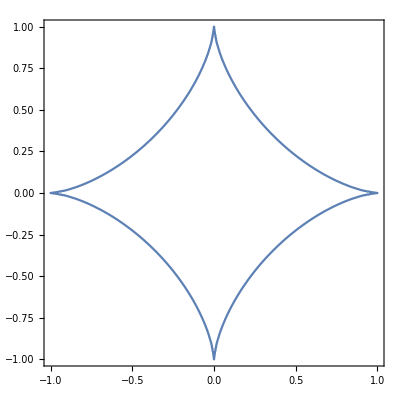

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,{x,-1,1},{y,-1,1}]
```

Summary
Given the refractive indices n_1 and n_2, object depth h, and incident angle θ_1, we can calculate
	θ_2=arcsin(n_1/n_2 sin θ_1)
	h'=h/n (1-u^2 tan^2 θ_1)^(3/2)	 where n=n_1/n_2 and u=√(n^2-1)
	x=h u^2 tan^3 θ_1.
Also, the image point lies on the astroid (h'/(h/n))^(2/3)+(x/(h/u))^(2/3)=1.

#### Verification (a bit old)

```mathematica
h=1.;
n=1.33;
θ1=35°;
θ2=ArcSin[n Sin@θ1];
hp=h/n Cos[θ2]^3/Cos[θ1]^3
hp=((1-(n^2-1)Tan[θ1]^2)^(3/2))/n
x=h Tan@θ1-hp Tan@θ2
x=h Tan[θ1]^3(n^2-1)
((n hp)/h)^(2/3)+((√(n^2-1)x)/h)^(2/3)
```

0.36974

0.36974

0.263967

0.263967

1.

### Section.Subsection Single point source

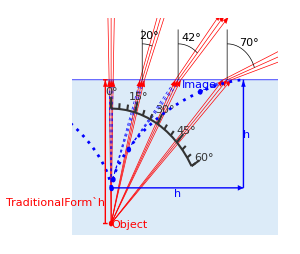

```mathematica
(*--------  User-defined parameters (play with these) ------*)
n1=1.33;n2=1;Z1=1./n1;Z2=1./n2;(* refractive indices of media *)
hO=1.;(* object depth *)
xO=0.;(* object horizontal position *)
rO={xO,-hO};
θ1List={0°,15°,30°,45°};
(*--------  Code ------*)
SetOptions[Graphics,BaseStyle->16];
rayLen=0.9;rayWid=0.5;rayHue=0.0;emergingRayLen=.6;objectDiskRadius=.02;
waterColor=RGBColor[{0.8627450980392157,0.9215686274509803,0.9725490196078431}];
grAH=Graphics[Line[{{-1,1},{2,0},{-1,-1}}]];
gr=Graphics[{
(*-------- water --------*)
{waterColor,Rectangle[{-999,0},{999,-999}],Blue,AbsoluteThickness@.5,Line@{{-999,0},{999,0}}},
(*-------- rays --------*)
AbsoluteThickness[rayWid],AbsolutePointSize@9,
δθ=1°;
Table[{
θ2Main=ArcSin[n1/n2*Sin[θ1Main]];
hI=hO(n2 Cos[θ2Main]^3)/(n1 Cos[θ1Main]^3);
xI=hO Tan[θ1Main]-hI*Tan[θ2Main];
Table[
θ2=ArcSin[n1/n2*Sin[θ1]];
rI={xI,-hI};
(*-------- rays --------*)
{
Arrowheads[{{.005,.5,grAH}}],
Hue[rayHue,1.0,1.0,1.0],Arrow[{{0,-hO},{hO Tan@θ1,0}}],(* incident ray *)
Arrowheads[{{.005,.3,grAH}}],
Hue[rayHue,1.0,1.0,1.0],Solid,Arrow[{{hO Tan@θ1,0},{hO Tan@θ1,0}+emergingRayLen *{Sin@θ2,Cos@θ2}}],(* refracted ray *)
Blue,AbsoluteDashing@{2,2},Line[{{xI,-hI},{hO Tan@θ1,0}}] (* virtual ray *),
}
,{θ1,{θ1Main-δθ,θ1Main,θ1Main+δθ}}],
(*-------- image point --------*)
Blue,Disk[rI,objectDiskRadius],
(*-------- angles and labels --------*)
Black,
r0={hO Tan@θ1Main,0};θ2=ArcSin[n1/n2*Sin@θ1Main];
If[θ2>0°,{
Line@{r0,r0+{0,.35}},  (* upward normal *)
Circle[r0,.25,{π/2-θ2,π/2}], (* arc *)
Text[StringForm["``°",Round[θ2/Degree]],r0+.32{Sin[θ2/2],Cos[θ2/2]}],(* refracted angle *)
}
]
},{θ1Main,θ1List}],
(*-------- protractor --------*)
radProtractor=.8;tickLenProtractor=.1radProtractor;minorTickLenProtractor=.05radProtractor;rS=rO;
GrayLevel@.2,AbsoluteThickness@1.5,
Circle[rS,radProtractor,{90°-60°,90°}],
Table[{
Line@{rS+radProtractor*{Sin@θ1,Cos@θ1},rS+(radProtractor+minorTickLenProtractor)*{Sin@θ1,Cos@θ1}},(* minor angular tick *)
},{θ1,0,60°,5°}],
Table[{
Line@{rS+radProtractor*{Sin@θ1,Cos@θ1},rS+(radProtractor+tickLenProtractor)*{Sin@θ1,Cos@θ1}}, (* major angular tick *),
Text[
StringForm["``°",θ1/Degree],
rS+(radProtractor+1.5tickLenProtractor)*{Sin@θ1,Cos@θ1}
]
},{θ1,0,60°,15°}],
(*-------- caustic curve --------*)
rCaustic=Table[
θ2=ArcSin[n1/n2*Sin[θ1]];
hI=hO(n2 Cos[θ2]^3)/(n1 Cos[θ1]^3);
xI=hO Tan[θ1]-hI*Tan[θ2];
rI={xI,-hI}
,{θ1,0.°,48.75°,.25°}];
{Blue,AbsoluteThickness@2.,AbsoluteDashing@{2,4},Line@rCaustic,Line@(rCaustic.({{-1, 0}, {0, 1}}))},
(*-------- dimension lines --------*)
Arrowheads[{{-.03,0},{.03,1}}],AbsoluteThickness@1,Blue,
Arrow@{{0,-hO/n1},{hO/(√(n1^2-1)),-hO/n1}},Arrow@{{hO/(√(n1^2-1)),-hO/n1},{hO/(√(n1^2-1)),0}},
Text["h",{.5 hO/(√(n1^2-1)),-hO/n1},{0,1.1}],
Text["h",{hO/(√(n1^2-1)),.5-hO/n1},{-1.1,0}],
Red,Arrow@{{-.05,-hO},{-.05,0}},Line@{{-.07,0},{-.03,0}},Line@{{-.07,-hO},{-.03,-hO}},
Text["TraditionalForm`h",{-.05,-.85},{1.5,0}],
(*-------- object points and image label --------*)
Red,Disk[rO,objectDiskRadius],Text["Object",rO,{-1.5,0}],
Blue,Text["Image",{.76,-.03},{0,0}]
},
BaseStyle->{12,FontFamily->"Times"},
Ticks->None,Axes->False,PlotRange->{{-.3,1.4},{-1.05,.4}},ImageSize->300(*,ImageMargins->0,ImagePadding->0*)
]
Export[NotebookDirectory[]<>"/ImageLocations.pdf",gr];
```

### Section.Subsection Interactive visualization

```mathematica
n1=1.33;n2=1;Z1=1./n1;Z2=1./n2;(* refractive indices of media *)
hO=1.;(* object depth *)
SetOptions[Graphics,BaseStyle->16];
rayLen=0.9;rayWid=1;rayHue=0.0;glassHue=0.5;
grAH=Graphics[Polygon[{{2,0},{-1,1},{-1,-1}}]];
Manipulate[
Graphics[{
Hue[glassHue,Tanh[(n1-1)/3.],1.0],Rectangle[{-999,0},{999,-999}],
Hue[glassHue,Tanh[(n2-1)/3.],1.0],Rectangle[{-999,0},{999,1}],
(*-------- Draw rays --------*)
Arrowheads[{{.005,.5,grAH}}],AbsoluteThickness[rayWid],AbsolutePointSize@9,
hObject=1.;
xObject=0;
δθ=2°;
θ1=θ1deg*Degree;θ2=ArcSin[n1/n2*Sin[θ1]];
hImage=hO(n2 Cos[θ2]^3)/(n1 Cos[θ1]^3);
xI=hO Tan[θ1]-hImage*Tan[θ2];
(*-------- old code below was for finding intersection of two rays --------*)
(*θ1m=θ1deg*Degree-δθ/2;θ2m=ArcSin[n1/n2*Sin[θ1m]];
θ1p=θ1deg*Degree+δθ/2;θ2p=ArcSin[n1/n2*Sin[θ1p]];*)
(*hImage=hObject*(Tan[θ1p]-Tan[θ1m])/(Tan[θ2p]-Tan[θ2m]);
xI=hObject*Tan[θ1p]-hImage*Tan[θ2p];*)

Table[
θ2=ArcSin[n1/n2*Sin[θ1]];
{
Hue[rayHue,1.0,1.0,1.0],Arrow[{{0,-hO},{hO Tan@θ1,0}}],(* incident ray *)
Hue[rayHue,1.0,1.0,1.0],Solid,Arrow[{{hO Tan@θ1,0},{hO Tan@θ1+hO Tan@θ2,hO}}],(* refracted ray *)
Hue[rayHue,1.0,1.0,1.0],Dashed,Line[{{hO Tan@θ1,0},{hO Tan@θ1-hO Tan@θ2,-hO}}] (* virtual ray *)
}
,{θ1,{θ1deg*Degree-δθ/2,θ1deg*Degree,θ1deg*Degree+δθ/2}}],
Black,
Disk[{xObject,-hObject},.015],Text["Object",{xObject,-hObject},{1.5,0}],
Circle[{xI,-hImage},.015],Text["Image",{xI,-hImage},{1.5,0}],
},
BaseStyle->12,
Ticks->None,Axes->True,AxesStyle->Directive@{Dashed,Black},PlotRange->{{-.5,1.8},{-1.1,.6}},ImageSize->500(*,ImageMargins->0,ImagePadding->0*)
],
{{θ1deg,30,"θ_1/°"},1,50,Appearance->"Open"},
ControlPlacement->Bottom,LabelStyle->16,TrackedSymbols:>True,FrameMargins->-3,AppearanceElements->None
]
```

Change the angle and see what happens to the image location!!!

### Section.Subsection Multiple points on extended object: magnification and distortion

-Graphics-

Consider the square object ABCD.  Apply the formulas to obtain the depths and horizontal displacements of all image points:
	h'_A=h_A ((1-u^2 tan^2 θ_1)^(3/2))/n		x_A=h_A u^2 tan^3 θ_1
	h'_B=h_B ((1-u^2 tan^2 θ_1)^(3/2))/n		x_B=h_B u^2 tan^3 θ_1.
Subtract:
	h_AB'=h'_B-h'_A=(h_B-h_A)((1-u^2 tan^2 θ_1)^(3/2))/n=h_AB((1-u^2 tan^2 θ_1)^(3/2))/n,
	x_AB'=x'_B-x'_A=(h_B-h_A)u^2 tan^3 θ_1=h_AB u^2 tan^3 θ_1.
So we have 
	M=h_AB'/h_AB=((1-u^2 tan^2 θ_1)^(3/2))/n		(vertical magnification).

## Section Image of a submerged object, given viewer position h_V

### Section.Subsection Single point: quartic equation - derivation. see RefractionSimulations.nb for demo

Suppose the viewer is located at r_V=(0,h_V) and the object point is located at r_O=(L,-h_O).
From the diagram...
-Graphics-

We have
	h_1 tan θ_1+h_2 tan θ_2=L		(trigonometry)
	n_1 sin θ_1=n_2 sin θ_2			(Snell).	
Given h_1,h_2,L,n_1,n_2, we wish to solve for θ_1 and θ_2.   Mathematica fails to do this directly.  We can coax Mathematica to give a solution by making substitutions.  

First let us non-dimensionalize.  Let p=h_1/L, q=h_2/L, n=n_1/n_2.  Then
	p tan θ_1+q tan θ_2=1
	n sin θ_1=sin θ_2
Let x=p tan θ_1=h_1/L tan θ_1 and y=q tan θ_2=h_2/L tan θ_2.  Then the two equations become
	x+y=1,
	n x/(√(p^2+x^2))=y/(√(q^2+y^2)).
From the second equation,
	n^2 x^2(q^2+y^2)=y^2(p^2+x^2)
∴	n^2 q^2 x^2+n^2 x^2 y^2=p^2 y^2+x^2 y^2
∴	n^2 q^2 x^2-p^2 y^2+(n^2-1)x^2 y^2=0.
Let a=p^2,b=n^2 q^2,u=n^2-1.  Then
	b x^2-a y^2+u x^2 y^2=0.
Substituting in y=1-x,
	b x^2-(a(1-x))^2+u(x^2(1-x))^2=0
∴	b x^2-a(1-2x+x^2)+u(x^2-2 x^3+x^4)=0
∴	u x^4-2u x^3+(u+b-a)x^2+2ax-a=0.
This is a good place to stop.

Given h_1,h_2,L,n_1,n_2, let x=h_1/L tan θ_1.  Then
calculate a=(h_1/L)^2,b=(n_1/n_2)^2(h_2/L)^2,and u=(n_1/n_2)^2-1, and find the root of u x^4-2u x^3+(u+b-a)x^2+2ax-a=0.  Then θ_1=arctan (L x)/h_1.

```mathematica
Clear[A,B,a,b,c,d,x,y,n,u,v];
x/.Solve[{x+y==1,(n  x)/(√(a+x^2))==y/(√(b/n^2+y^2))},{x,y},Quartics->False]⟦1⟧/.n^2->u+1//FullSimplify
```

1-Root[b-2 b #1+(-a+b+u) #1^2-2 u #1^3+u #1^4&,1]

Further let g=u+b-a=n^2-1+n^2 q^2-p^2.  Then
	u x^4-2u x^3+g x^2+2ax-a=0.
Finally, let g=uv and a=uw and divide throughout by u to obtain
	x^4-2 x^3+v x^2+2wx-w=0
where v=g/u=(n^2-1+n^2 q^2-p^2)/(n^2-1)=1+(n^2 h_2^2-h_1^2)/((n^2-1)L^2)=1+(n_1^2 h_2^2-n_2^2 h_1^2)/((n_1^2-n_2^2)L^2) and w=a/u=1/(n^2-1)h_1^2/L^2.

Given h_1,h_2,L,n_1,n_2, calculate v=1+(n_1^2 h_2^2-n_2^2 h_1^2)/((n_1^2-n_2^2)L^2) and w=(n_2^2 h_1^2)/((n_1^2-n_2^2)L^2), and find the root of x^4-2 x^3+v x^2+2wx-w=0.  Then θ_1=arctan (L x)/h_1.

```mathematica
x/.Solve[x^4-2 x^3+v x^2+2w x-w==0,{x},Quartics->True]⟦1⟧
```

#### Alternatives

Let s=sin θ_1, t=sin θ_2.  Thus 
	A s/(√(1-s^2))+B t/(√(1-t^2))=1
	ns=t.
Eliminate t:
	A s/(√(1-s^2))+B ns/(√(1-n^2 s^2))=1
∴	As √(1-n^2 s^2)+Bns √(1-s^2)=√(1-n^2 s^2)√(1-s^2)
∴	(As √(1-n^2 s^2)+Bns √(1-s^2))^2=(1-n^2 s^2)(1-s^2)
∴	A^2 s^2(1-n^2 s^2)+B^2 n^2 s^2(1-s^2)+2ABn s^2 √(1-n^2 s^2)√(1-s^2)=1-n^2 s^2-s^2+n^2 s^4
∴	A^2 s^2(1-n^2 s^2)+B^2 n^2 s^2(1-s^2)-1+n^2 s^2+s^2-n^2 s^4=2ABn s^2 √(1-n^2 s^2)√(1-s^2)
∴	[A^2 s^2(1-n^2 s^2)+B^2 n^2 s^2(1-s^2)-1+n^2 s^2+s^2-n^2 s^4]^2=4 A^2 B^2 n^2 s^4(1-n^2 s^2)(1-s^2)
∴	[as^2(1-u s^2)+bs^2(1-s^2)-1+u s^2+s^2-u s^4]^2=4abs^4(1-n^2 s^2)(1-s^2)	where a=A^2,b=B^2 n^2,u=n^2.
Lengthy algebra turns this into a quartic equation in s^2.  This equation can be solved algebraically for s.  One can then compute θ_1=arcsin s and θ_2=arcsin(n_1/n_2 sin θ_1).  One is then in a position to apply the previously derived formulas to compute h and x.

```mathematica
Clear[a,b,u,s];
Solve[1+t (-2-2 a-2 b-2 u)+t^2 (1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2)+t^3 (-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2)+t^4 (b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2)==0,{t},Quartics->False]
```

{{t→Root[1+(-2-2 a-2 b-2 u) #1+(1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2) #1^2+(-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2) #1^3+(b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2) #1^4&,1]},{t→Root[1+(-2-2 a-2 b-2 u) #1+(1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2) #1^2+(-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2) #1^3+(b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2) #1^4&,2]},{t→Root[1+(-2-2 a-2 b-2 u) #1+(1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2) #1^2+(-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2) #1^3+(b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2) #1^4&,3]},{t→Root[1+(-2-2 a-2 b-2 u) #1+(1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2) #1^2+(-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2) #1^3+(b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2) #1^4&,4]}}

### Section.Subsection Numerical application to several points with fish texture

```mathematica
fish=-Graphics-;fishTexture=Texture[fish];
```

```mathematica
(*--------  User-defined parameters (play with these) ------*)
n1=1.33;n2=1;Z1=1./n1;Z2=1./n2;(* refractive indices of media *)
xV=1.3;                                    (* viewer's eye horizontal position *)
hV=0.3;                                    (* viewer's eye elevation above water surface *)
xOCenter=0.3; (* horizontal position of CoM of rectangular object *)
hOCenter=0.8; (* -vertical position of CoM of rectangular object *)
objectSize=0.4;(* extent of object *)

(*--------- Code ----*)
solveQuarticProblem[L_,h1_,h2_,n1_,n2_]:=Module[{a,b,u,sSquared,θ1},
a=(h1/L)^2;b=(h2/L)^2(n1/n2)^2;u=(n1/n2)^2;
sSquared=Root[1+(-2-2 a-2 b-2 u) #1+(1+2 a+a^2+4 b-2 a b+b^2+4 u+4 a u+2 b u+u^2) #1^2+(-2 b+2 a b-2 b^2-2 u-4 a u-2 a^2 u-4 b u+2 a b u-2 u^2-2 a u^2) #1^3+(b^2+2 b u-2 a b u+u^2+2 a u^2+a^2 u^2) #1^4&,1];
θ1=ArcSin[√sSquared];
Return@θ1;
];
waterColor=RGBColor[{0.8627450980392157,0.9215686274509803,0.9725490196078431}];
rayLen=0.9;rayWid=0.5;rayHue=0.0;
grAH=Graphics[Line[{{-1,1},{2,0},{-1,-1}}]];
rV={xV,hV};
rOList={};rIList={};
gr=Graphics[{
(*-------- water --------*)
waterColor,Rectangle[{-999,0},{999,-999}],
(*-------- manual gridlines -------*)
GrayLevel@.8,
Line@Table[{{x,-99},{x,99}},{x,Range[-2.5,2.5,.1]}],
Line@Table[{{-99,z},{99,z}},{z,Range[-2.5,2.5,.1]}],
(*-------- rays --------*)
Arrowheads[{{.007,.5,grAH}}],AbsoluteThickness[rayWid],AbsolutePointSize@9,
Table[{
θ1=solveQuarticProblem[xV-xO,hO,hV,n1,n2];    (* calculate angles *)
θ2=ArcSin[n1/n2*Sin[θ1]];
hI=hO(n2 Cos[θ2]^3)/(n1 Cos[θ1]^3);xI=hO Tan[θ1]-hI*Tan[θ2];    (* locate image *)
rV={xV,hV};rO={xO,-hO};rI={xO+xI,-hI};rS={xO+hO Tan[θ1],0};rS={xV-hV Tan[θ2],0};
AppendTo[rOList,rO];
AppendTo[rIList,rI];
(*-------- rays -------*)
If[xO!=xOCenter&&hO≠hOCenter,{
Hue@rayHue,Arrow[{rO,rS}],(* incident ray *)
Hue@rayHue,Arrow[{rS,rV}],(* refracted ray *)
Blue,Dashed,Line[{rI,rS}] (* virtual ray *)
}]
},
{xO,xOCenter+{-.5objectSize,0,+.5objectSize}},  (* horizontal coordinates of object points *)
{hO,hOCenter+{-.5objectSize,0,+.5objectSize}}  (* vertical coordinates of object points *)
],
(*-------- draw actual fish and image fish -------*)
Opacity[1],
fishTexture,Polygon[rOList⟦{3,9,7,1}⟧,VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
fishTexture,Polygon[rIList⟦{3,9,7,1}⟧,VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
(*-------- draw viewer and object and object and image points -------*)
Black,Disk[rV,.015],Text["Viewer",rV,{+1.5,0}],
{
Opacity[.5,Black],
Line@{rOList⟦{3,6,9}⟧,rOList⟦{2,5,8}⟧,rOList⟦{1,4,7}⟧,rOList⟦{1,2,3}⟧,rOList⟦{4,5,6}⟧,rOList⟦{7,8,9}⟧},
Line@{rIList⟦{3,6,9}⟧,rIList⟦{2,5,8}⟧,rIList⟦{1,4,7}⟧,rIList⟦{1,2,3}⟧,rIList⟦{4,5,6}⟧,rIList⟦{7,8,9}⟧}
},
Red,Text["Object",Mean@rOList,{-3.3,5}],Disk[#,.01]&/@rOList,
Blue,Text["Image",Mean@rIList,{+2.2,-1}],Disk[#,.01]&/@rIList
},
BaseStyle->{16,Bold,FontFamily->"Times"},LabelStyle->{16,Black,FontFamily->"Times",FontWeight->"Plain"},
PlotRange->{{-0.15,1.4},{-1.05,0.3}},AxesStyle->{Black,FontFamily->"Times",FontWeight->"Plain"},
AxesLabel->{"x (m)","y (m)"//Style[#,Black]&},
Ticks->Automatic,Axes->True,ImageSize->400
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/Distortion.pdf",gr];
```

## Appendix (testing graphics code)

### Section.Subsection TextTexture demo

```mathematica
myTexture="plane of incidence"//Style[#,Blue]&//Text//Rasterize[#,ImageSize->{256,256},Background->None]&//Texture;
Graphics3D[{
FaceForm[Pink],Polygon[{{-1,-1,-1.1},{1,-1,-1},{1,1,-1},{-1,1,-1}}],   (* substrate must be a little BEHIND the text plane *)
myTexture,Polygon[{{-1,-1,-1},{1,-1,-1},{1,1,-1},{-1,1,-1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
},
Boxed->True
]
```

### Section.Subsection 3D arrowheads

```mathematica
myAH=Graphics3D[Cone[{{0,0,0},{.2,0,0}},.1]];
Graphics3D[{
(*-------- Incident, reflected, refracted rays --------*)
Lighter@Purple,
CapForm["Butt"],
Arrowheads[{{
.2,1,{myAH,0}  (* no need to foreshorten shaft???? *)
}}],  
Arrow@Tube[{{0,0,0},{-1,1,1}},.1]

},Lighting->{
{"Ambient",GrayLevel[.7]},
{"Directional",White,{{5,5,4},{0,0,0}}},
{"Spot",White,{{2,2,20},{0,0,0}},Pi/6}
},
ViewPoint->{0.5,-1,.5},ViewVertical->{0,0,1},ViewAngle->35°,
PlotRange->All,PlotRangePadding->2,Boxed->False,ImageSize->{768,512},
BaseStyle->{36,Bold}
]
```

## Setup (autorun)

### Section.Subsection Graphics options (autorun)

```mathematica
Solid=Dashing@{};
Thickness1=AbsoluteThickness@1;
DarkGreen=Darker[Green,0.67];
resistorColorList={Black,Brown,Red,Orange,Darker@Yellow,Darker@Green,Blue,Purple,Gray,Cyan};
resistorStyle[n_Integer]:={AbsoluteThickness@1,resistorColorList[[Mod[n,Length@resistorColorList,1]]]};
alternateColorList={Red,Darker@Green,Blue,Darker@Cyan,Magenta,Darker@Yellow,Gray,Black};
alternateStyles=({AbsoluteThickness@1,#}&/@alternateColorList);
blackStyles={{AbsoluteThickness@1,Black},{Dotted,Gray}};
myStyles=({AbsoluteThickness@1,#}&/@resistorColorList);
purpleWhite[v_]:=Hue[0.75,0.25,Abs[v]^0.5];
blueWhiteRed[v_]:=Hue[If[v>0.5,0.0,0.5],(2Abs[v-0.5]),0.95];
colorFromComplex[z_,OptionsPattern[{Brightness->1.}]]:=Hue[Rescale[Arg@z,{0,2 π}],0.8,Tanh@Abs[z*OptionValue[Brightness]]];
manualColor[zmin_,zmax_]:=ColorFunction->(ColorData["FuchsiaTones"][Rescale[#,{zmin,zmax}]]&);
myGS={BaseStyle->{16,FontFamily->"Times"},FrameStyle->Directive@{AbsoluteThickness@0,Black}};
myPS={ImageSize->192,(*PlotStyle->myStyles,*)
LabelStyle->{16,FontFamily->"Times",Black},RotateLabel->False};
SetOptions[Graphics,myGS];
SetOptions[Plot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ParametricPlot,myGS,myPS,ExclusionsStyle->Automatic];
SetOptions[ListPlot,myGS,myPS];
SetOptions[ListLogPlot,myGS,myPS];
SetOptions[ListLogLogPlot,myGS,myPS];
SetOptions[ListLogLinearPlot,myGS,myPS];
SetOptions[StreamPlot,myGS];
enlargeFont=#/.s_String->Style[s,16]&;
SetOptions[Graphics3D,PlotRange->All,ImageSize->600,ViewPoint->{-1,-2,1},ViewVertical->{0,0,1},Lighting->"Neutral",Boxed->False,AspectRatio->Automatic];
```

### Section.Subsection Graphics utilities: enlargeFont, makeLineLegend, arrayPlot, colorBar, myBarChart, mySmoothedBarChart (autorun)

```mathematica
(*enlargeFont=Module[{s},(#/.s_String->Style[s,FontFamily->"Times",20]&)];*)
enlargeFont=#1/.s_String->Style[s,24]&;
makeLineLegend[styles_,labels_,OptionsPattern[{LegendPosition->{0.75,0.75},LegendImageSize->64}]]:=
Module[{trimmedStyles,trimmedLabels,numKeys},
(*----- Idiot-proofing -----*)
numKeys=Min[Length@styles,Length@labels];
trimmedStyles=styles[[1;;numKeys]];
trimmedLabels=labels[[1;;numKeys]];
(*----- Generate the graphics -----*)
Graphics@Inset[#,Scaled@OptionValue@LegendPosition]&@Grid[MapThread[{Graphics[{Directive@#1,Line@{{-1,0},{1,0}}},ImageSize->OptionValue@LegendImageSize,AspectRatio->0.01],#2}&,{trimmedStyles,trimmedLabels}],Alignment->Left]
];
makeLineLegend2[styles_,labels_]:=
Module[{trimmedStyles,trimmedLabels,numKeys},
(*----- Idiot-proofing -----*)
numKeys=Min[Length@styles,Length@labels];
trimmedStyles=styles[[1;;numKeys]];
trimmedLabels=labels[[1;;numKeys]];
(*----- Generate the graphics -----*)
Graphics@Text@Grid[
MapThread[{Graphics[{Directive@#1,Line@{{-1,0},{1,0}}},AspectRatio->0.01,ImageSize->24],#2}&,{trimmedStyles,trimmedLabels}],Alignment->Left,Spacings->0]
];
makeLineLegend2::usage="makeLineLegend2[{style1, style2, ...},{label1, label2, ...}]
 returns a legend consisting of styled lines and labels.  This legend is a Graphics object.";
```

```mathematica
Options[arrayPlot]=Join[{},Options@Plot];
arrayPlot$ImagePadding={{36,8},{44,8}};
arrayPlot[gxy_,opts:OptionsPattern[]]/;ArrayDepth@gxy==2:=
Module[{l,r,b,t,ll=0,rr=64,w=192,h,xmax,ymax,cf},
(*---- Extract options ----*)
{{l,r},{b,t}}=arrayPlot$ImagePadding;
{gmin,gmax}=arrayPlot$ZRange;
{xmax,ymax}=Dimensions[gxy];
neato`DensityPlotHeight=h=Round[w*ymax/xmax];(* choose image height acc/to aspect ratio of data, and save in GLOBAL variable! *)
ArrayPlot[gxy//Transpose//Reverse,
ColorFunction->(arrayPlot$ColorFunction@Rescale[#,arrayPlot$ZRange,{0,1}]&),ColorFunctionScaling->False,
FilterRules[{opts},Options@ArrayPlot],
FrameLabel->Reverse@{"\!\(\*
StyleBox[\"x\",\nFontSlant→\"Italic\"]\)","\!\(\*
StyleBox[\"y\",\nFontSlant→\"Italic\"]\)"},RotateLabel->False,
(*FrameTicks->Reverse@{{1,Floor[xmax/2],xmax},{1,Floor[ymax/2],ymax}},*)
DataRange->{{1,xmax},{1,ymax}},
ImageSize->{w+l+r,h+b+t},ImagePadding->{{l,r},{b,t}}
]
];
Options[colorBar]=Join[{},Options@Plot];
colorBar[opts:OptionsPattern[]]:=
Module[{l,r,b,t,ll=0,rr=64,ww=24,w=192,h,xmax,ymax,ngmax=50},
{{l,r},{b,t}}=arrayPlot$ImagePadding;
h=neato`DensityPlotHeight;(* read global variable  *)
ArrayPlot[Table[Rescale[ng,{1,ngmax},arrayPlot$ZRange],{ng,1,ngmax},{ndummy,2}]//Reverse,
ColorFunction->(arrayPlot$ColorFunction@Rescale[#,arrayPlot$ZRange,{0,1}]&),ColorFunctionScaling->False,
FilterRules[{opts},Options@ArrayPlot],
DataRange->{All,arrayPlot$ZRange},
FrameTicks->{None,None,Union[arrayPlot$ZRange,FindDivisions[arrayPlot$ZRange,4]]//N,None},
ImageSize->{ww+ll+rr,h+b+t},ImagePadding->{{ll,rr},{b,t}}]
];
```

```mathematica
arrayPlot[gxyz_,opts:OptionsPattern[]]/;ArrayDepth@gxyz==3:=
Module[{l,r,b,t,ll=0,rr=64,w=192,h,xmax,ymax,zmax,cf},
(*---- Extract options ----*)
{{l,r},{b,t}}=arrayPlot$ImagePadding;
{gmin,gmax}=arrayPlot$ZRange;
{xmax,ymax,zmax}=Dimensions[gxyz];
neato`DensityPlotHeight=h=Round[w*ymax/xmax];(* choose image height acc/to aspect ratio of data, and save in GLOBAL variable! *)

GraphicsRow[Table[
ArrayPlot[gxyz[[All,All,z]]//Transpose//Reverse,
ColorFunction->(arrayPlot$ColorFunction@Rescale[#,arrayPlot$ZRange,{0,1}]&),ColorFunctionScaling->False,
FilterRules[{opts},Options@ArrayPlot],
DataRange->{{1,xmax},{1,ymax}},
ImageSize->{w+0+1,h+0+1},ImagePadding->{{0,1},{1,1}}
],{z,zmax}],Spacings->0]
];
```

```mathematica
Options[myBarChart]={}~Join~Options@Plot;
myBarChart[ξCategories_,Aξ_,opts:OptionsPattern[]]:=Module[{points,nξmax},
nξmax=Length@Aξ;
points=Join[
{{ξCategories[[1]],0}},
Join@@Table[{{ξCategories[[nξ]],Aξ[[nξ]]/(ξCategories[[nξ+1]]-ξCategories[[nξ]])},{ξCategories[[nξ+1]],Aξ[[nξ]]/(ξCategories[[nξ+1]]-ξCategories[[nξ]])}},{nξ,nξmax}],
{{ξCategories[[nξmax+1]],0}}
];
ListPlot[points,
Joined->True,
FilterRules[{opts}, Options@Plot],
PlotRange->All,Filling->Axis]
];
(*-------- To smear a PDF (prob. dist. func.) without spoiling sum rule, we should smear the CDF. --------*)
Options[mySmoothedBarChart]={}~Join~Options@Plot;
mySmoothedBarChart[ξCategories_,Aξ_,opts:OptionsPattern[]]:=Module[{points,nξmax},
cdf=FoldList[Plus,0,Aξ];  (*cumulative distribution*)
cdfInterpolated=Interpolation[Transpose@{ξCategories,cdf},InterpolationOrder->5];  (*find cubic interpolant to CDF*)
pdfSmoothed[x_]=D[cdfInterpolated[x], x];
Plot[pdfSmoothed[x],{x,Min[ξCategories],Max[ξCategories]},
FilterRules[{opts}, Options@Plot],PlotRange->All]
];
```

```mathematica
myDensityPlot[func_,{x_,xmin_,xmax_,xpoints_},{y_,ymin_,ymax_,ypoints_},opts:OptionsPattern[]]:=
arrayPlot[
Table[func[x,y],
{x,Rescale[Range[xpoints],{1,xpoints},{xmin,xmax}]},
{y,Rescale[Range[ypoints],{1,ypoints},{ymin,ymax}]}
],
ImageSize->{256+64+8,256+64+32},ImagePadding->{{64,8},{64,32}},opts,
PlotRange->All,PlotRangePadding->None,DataRange->{{xmin,xmax},{ymin,ymax}},
(*FrameTicks->{All,All,None,None}*)
FrameTicks->{Automatic,Automatic,None,None}
];
```